# Simon’s Algorithm

Episode 29. Deutsch-Jozsa Algorithm

Episode 30. Bernstein-Vazirani Algorithm

Episode 31. Simon’s Algorithm

## Statement of the Problem

We are given a function f:{0, 1}^n→{0, 1}^n and a secret string s of n bits.

For all x,y∈{0,1}^n, f(x)=f(y) if and only if y=x⊕s. Note that f is either one-to-one (s=0) or two-to-one (s≠0).

The task is to find the secret string s with as few queries to function f as possible.

Classically, one needs queries to f(x) with up to 2^(n-1)+1 different inputs.

## Quantum Implementation

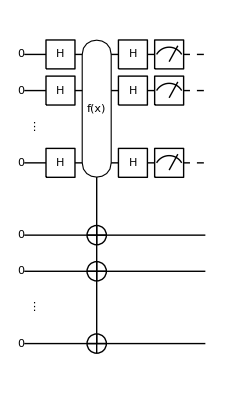

Figure 1. A quantum circuit to implement Simon's algorithm.

The quantum circuit in Figure 1 summarizes Simon’s algorithm. The first Hadamard gate on the native register transforms the input state of the whole system as

0⊗0→^(H^(⊗n))1/2^(n/2)Σ_(x=0)^(2^n-1)x⊗0.

The quantum oracle makes a copy of the image f(x) of the state x of the native register to the ancillary register, and leads to

1/2^(n/2)Σ_(x=0)^(2^n-1)x⊗f(x) .

Finally, the second set of Hadamard gates on the native register maps the above state into

Σ_(y=0)^(2^n-1)y⊗1/2^n Σ_(x=0)^(2^n-1)(f(x)(-1))^(x·y) .

The measurement on the native register yields an n-bit string y.

The probability for a particular string y is determined by the squared norm,

P_y=ψ_yψ_y,

of the y-dependent state ψ_y of the ancillary register

ψ_y:=1/2^n Σ_(x=0)^(2^n-1)(f(x)(-1))^(x·y) .

For s=0, function f is one-to-one.

ψ_y:=1/2^n Σ_(x=0)^(2^n-1)(f(x)(-1))^(x·y)=1/2^n Σ_(z=0)^(2^n-1)(z(-1))^(f^-1(z)·y) .

P_y=1/2^n

For the analysis of the quantum circuit, see Section 4.2.4 of the Quantum Workbook (2022, 2023) or the Q3 tutorial “Simon’s Algorithm”.

## Examples

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

### Smaller System

Consider again a secrete bit string.

```mathematica
string={1,1};
```

Consider a two-to-one function obeying the rule (specified in Simon’s problem).

```mathematica
Clear[f];
f[{0,0}]=f[{1,1}]={0,1};
f[{0,1}]=f[{1,0}]={1,1};
```

Here is an implementation of the corresponding quantum oracle.

```mathematica
cc={1,2};
tt={3,4};
all=Join[cc,tt];
qc=QuantumCircuit[Ket[S@all],S[cc,6],Oracle[f,S@cc,S@tt],S[cc,6],Measurement[S[cc,3]],
"Invisible"->S@{2.5}]
```

```mathematica
out=ExpressionFor[qc]
result=Readout[S[cc,3]]
```

```mathematica
mat=Table[ExpressionFor[qc];Readout[S[cc,3]],{2}]
```

### Larger System

Now, let us examine a lager system. Suppose that we are given a secrete bit string.

```mathematica
string={1,1,0};
```

This is a function consistent with the above secrete bit string.

```mathematica
Clear[f];
f[0]=f[6]=3;
f[1]=f[7]=7;
f[2]=f[4]=4;
f[3]=f[5]=1;
```

Here is an implementation of the corresponding quantum oracle.

```mathematica
cc={1,2,3};
tt={4,5,6};
all=Join[cc,tt];
qc1=QuantumCircuit[Ket[S@all],S[cc,6],Oracle[f,S@cc,S@tt],S[cc,6]];
qc2=QuantumCircuit[qc1,Measurement[S[cc,3]],
"Invisible"->S@{3.5}]
```

This is one way to get the measurement outcome.

```mathematica
out=ExpressionFor[qc2]
result=Readout[S[cc,3]]
```

To make repeated measurements, it is more efficient to first compute the state just before the measurement.

```mathematica
new=ExpressionFor[qc1];
```

Now we perform the measurement repeatedly.

```mathematica
data=Table[Measurement[S[cc,3]]@new;Readout[S[cc,3]],{12}];
data//TableForm
```

As two linearly independent vectors (bit strings), we choose these:

```mathematica
mat={{1,1,0},{0,0,1}}
```

Then, the linear equation, mat.ss=0 (mod 2), for the Boolean variables ss:={s1,s2,s3} is given by the following, which agrees with the given secrete bit string.

```mathematica
ss={1,1,0}
```

```mathematica
Mod[mat.ss,2]
```

## Summary

### Keywords

Oracle

Decision making

Simon’s problem

### Functions

Oracle

### Related Links

Section 4.2 of the Quantum Workbook (2022, 2023).

Tutorial: Simon's Algorithm